```mathematica
<<"/home/rob/lean/mathematica_examples/_target/deps/mathematica/src/server2.m"
```

```mathematica
MakeDataUrlFromFile[filename_] :=
"data:image/png;base64,"<>(ReadByteArray[filename]//BaseEncode //ToString)
```

```mathematica
MakeDataUrlFromImage[img_] :=
Module[
{tempFile=CreateTemporary[]<>".png.b64",
 out},
Export[tempFile,img];
out = "data:image/png;base64,"<>StringDelete[ReadString[tempFile],"\n"];
CopyToClipboard[out];
out]
```

```mathematica
Foo[x]+4/.Foo[x]->3
```

7

```mathematica
PlotOverX[f_,{X_,lb_,ub_}] := Module[{nv,re},
re =f/.X->nv; Plot[re,{nv,lb,ub}]]
```

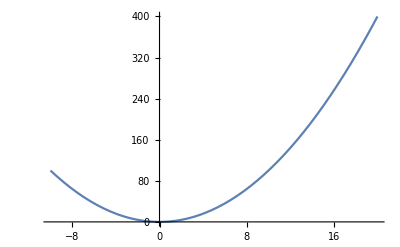

```mathematica
PlotOverX[Foo[x]^2,{Foo[x],-10,20}]
```

```mathematica
nv
```

nv

```mathematica
lb
```

lb

```mathematica
ub
```

ub

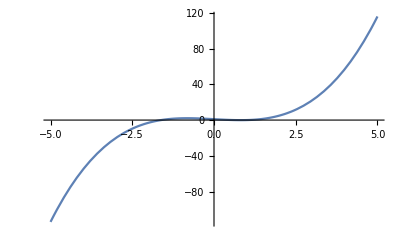
MakeDataUrlFromImage[-Graphics-]

```mathematica
MakeDataUrlFromImage[PlotOverX[Activate[LeanForm[LeanApp[LeanApp[LeanApp[LeanApp[LeanConst[LeanNameMkString["add",LeanNameMkString["has_add",LeanNameAnonymous]],LeanLevelListCons[LeanZeroLevel,LeanLevelListNil]],LeanConst[LeanNameMkString["int",LeanNameAnonymous],LeanLevelListNil]],LeanConst[LeanNameMkString["has_add",LeanNameMkString["int",LeanNameAnonymous]],LeanLevelListNil]],LeanApp[LeanApp[LeanApp[LeanApp[LeanConst[LeanNameMkString["sub",LeanNameMkString["has_sub",LeanNameAnonymous]],LeanLevelListCons[LeanZeroLevel,LeanLevelListNil]],LeanConst[LeanNameMkString["int",LeanNameAnonymous],LeanLevelListNil]],LeanConst[LeanNameMkString["has_sub",LeanNameMkString["int",LeanNameAnonymous]],LeanLevelListNil]],LeanApp[LeanApp[LeanApp[LeanApp[LeanApp[LeanConst[LeanNameMkString["pow",LeanNameMkString["has_pow",LeanNameAnonymous]],LeanLevelListCons[LeanZeroLevel,LeanLevelListCons[LeanZeroLevel,LeanLevelListNil]]],LeanConst[LeanNameMkString["int",LeanNameAnonymous],LeanLevelListNil]],LeanConst[LeanNameMkString["nat",LeanNameAnonymous],LeanLevelListNil]],LeanApp[LeanApp[LeanConst[LeanNameMkString["has_pow",LeanNameMkString["monoid",LeanNameAnonymous]],LeanLevelListCons[LeanZeroLevel,LeanLevelListNil]],LeanConst[LeanNameMkString["int",LeanNameAnonymous],LeanLevelListNil]],LeanConst[LeanNameMkString["monoid",LeanNameMkString["int",LeanNameAnonymous]],LeanLevelListNil]]],LeanConst[LeanNameMkString["x",LeanNameAnonymous],LeanLevelListNil]],LeanApp[LeanApp[LeanApp[LeanApp[LeanConst[LeanNameMkString["bit1",LeanNameAnonymous],LeanLevelListCons[LeanZeroLevel,LeanLevelListNil]],LeanConst[LeanNameMkString["nat",LeanNameAnonymous],LeanLevelListNil]],LeanConst[LeanNameMkString["has_one",LeanNameMkString["nat",LeanNameAnonymous]],LeanLevelListNil]],LeanConst[LeanNameMkString["has_add",LeanNameMkString["nat",LeanNameAnonymous]],LeanLevelListNil]],LeanApp[LeanApp[LeanConst[LeanNameMkString["one",LeanNameMkString["has_one",LeanNameAnonymous]],LeanLevelListCons[LeanZeroLevel,LeanLevelListNil]],LeanConst[LeanNameMkString["nat",LeanNameAnonymous],LeanLevelListNil]],LeanConst[LeanNameMkString["has_one",LeanNameMkString["nat",LeanNameAnonymous]],LeanLevelListNil]]]]],LeanApp[LeanApp[LeanApp[LeanApp[LeanConst[LeanNameMkString["mul",LeanNameMkString["has_mul",LeanNameAnonymous]],LeanLevelListCons[LeanZeroLevel,LeanLevelListNil]],LeanConst[LeanNameMkString["int",LeanNameAnonymous],LeanLevelListNil]],LeanConst[LeanNameMkString["has_mul",LeanNameMkString["int",LeanNameAnonymous]],LeanLevelListNil]],LeanApp[LeanApp[LeanApp[LeanConst[LeanNameMkString["bit0",LeanNameAnonymous],LeanLevelListCons[LeanZeroLevel,LeanLevelListNil]],LeanConst[LeanNameMkString["int",LeanNameAnonymous],LeanLevelListNil]],LeanConst[LeanNameMkString["has_add",LeanNameMkString["int",LeanNameAnonymous]],LeanLevelListNil]],LeanApp[LeanApp[LeanConst[LeanNameMkString["one",LeanNameMkString["has_one",LeanNameAnonymous]],LeanLevelListCons[LeanZeroLevel,LeanLevelListNil]],LeanConst[LeanNameMkString["int",LeanNameAnonymous],LeanLevelListNil]],LeanConst[LeanNameMkString["has_one",LeanNameMkString["int",LeanNameAnonymous]],LeanLevelListNil]]]],LeanConst[LeanNameMkString["x",LeanNameAnonymous],LeanLevelListNil]]]],LeanApp[LeanApp[LeanConst[LeanNameMkString["one",LeanNameMkString["has_one",LeanNameAnonymous]],LeanLevelListCons[LeanZeroLevel,LeanLevelListNil]],LeanConst[LeanNameMkString["int",LeanNameAnonymous],LeanLevelListNil]],LeanConst[LeanNameMkString["has_one",LeanNameMkString["int",LeanNameAnonymous]],LeanLevelListNil]]]]],{Activate[LeanForm[LeanConst[LeanNameMkString["x",LeanNameAnonymous],LeanLevelListNil]]],-5,5}]]
```